# Simplex 2D ICS Optimisation

Simplex Optimisation Notes
NelderMead is the name of the simplex routine in mathematica to distinguish it from the simplex linear programming routine.
https://reference.wolfram.com/language/tutorial/ConstrainedOptimizationGlobalNumerical.html and search simplex for documentation.
An overview ofd this method can be found in my thesis.

This is a simplex optimisation, where the transverse profile of the electron bunch is not round i.e ϵ_xand ϵ_y can vary from each other and so can the corresponding β-functions. 
The aim is to maximise the collimated flux (my derivation) with in a specified bandwidth (single point optimisation) or for a range of bandwidths (tuning curve optimisation), and can also be conducted for a FWHM bandwidth.

NOTE
The optimisation can sometimes fail to converge for small emittances and large energy spreads where the optimisation gets ‘trapped’ in a local minima.

## Setup

## Units + Constants

```mathematica
(*Units*)
```

```mathematica
MeV=10^6;
nm=10^-9;
mm=10^-3;
mrad=10^-3;
μrad=10^-6;
nrad=10^-9;
μm=10^-6;
pC=10^-12;
nC=10^-9;
μJ=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
```

```mathematica
me=0.51099895MeV;
h=4.135667696*10^-15; (*in eV*)
clight=299792458;
echarge=1.60217662*10^-19;
σT=6.6524587158*10^-29;
re=2.8179403262*10^-15;
fivedeg=(5*π)/180;
```

## Cases

```mathematica
(*NEW DIANA*)
DIANA362={Ee->362MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->6.57*10^-4};
DIANA717={Ee->717MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->6.57*10^-4};
DIANA1072={Ee->1072MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->6.57*10^-4};
```

```mathematica
(*Opt + Char Cases*)
CaseA={Ee->1000MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->30μm,tpulse->10ps,σze->1mm,f->100MHz,ΔEe->10^-4,Δλ->4.66*10^-4};
CaseB={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->3nC,Epulse->100μJ,ϵnx->18.78mm mrad,ϵny->0.233mm mrad,σL->30μm,tpulse->10ps,σze->27.9mm,f->83.33MHz,ΔEe->6.07*10^-4,Δλ->4.66*10^-4};
CaseC={Ee->25MeV,λ->1064nm,ϕ->fivedeg,Q->10pC,Epulse->100μJ,ϵnx->0.1mm mrad,ϵny->0.1mm mrad,σL->30μm,tpulse->10ps,σze->0.38mm,f->100MHz,ΔEe->3*10^-4,Δλ->4.66*10^-4};
```

```mathematica
(*OLD? FEBE ICS*)
FEBE250={Ee->250MeV,λ->800nm,ϕ->fivedeg,Q->100pC,Epulse->0.1,ϵnx->5mm mrad,ϵny->5mm mrad,σL->45 μm,tpulse->2ps,σze->0.72mm,f->1,ΔEe->4*10^-6,Δλ->0.03185};
```

```mathematica
trialcase=CaseC;
```

## Base Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(h*clight)/λ;
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.trialcase
```

11587.3

## Lorentz Invariants (from Mandelstam Variables)

```mathematica
X[Ee_,ϕ_,λ_]:=(2*γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

```mathematica
X[Ee,ϕ,λ]/.trialcase
```

0.000454466

```mathematica
Y[Ee,ϕ,λ,0]/.trialcase
```

0.000454256

## Cross Section

## Cross Section [Berestetskii, σ = f(Y)]

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

```mathematica
dσdY[Ee,ϕ,λ,0]/.trialcase
```

5.03291×10^-22

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol},Method->"Trapezoidal"];
```

```mathematica
σ[Ee,ϕ,λ,0.5mrad]/.trialcase//AbsoluteTiming
```

{0.0302232,6.8246×10^-32}

## Luminosity

## Luminosity Intermediaries

```mathematica
(*Luminosity equations*)
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
```

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIPx,ϵnx,Ee,σL]*convxy[βIPy,ϵny,Ee,σL]);
```

```mathematica
L[Ee,λ,Q,Epulse,0.1,0.1,ϵnx,ϵny,σL]/.trialcase
```

4.83572×10^30

## Angular Crossing + Hourglass Effect (Miyahara)

```mathematica
H[ϕ_,βIPx_,βIPy_,Ee_,ϵnx_,ϵny_,σL_,σze_,tpulse_]:=Cos[ϕ]*Sqrt[(convxy[βIPx,ϵnx,Ee,σL]^2*convxy[βIPy,ϵny,Ee,σL]^2)/(π*convz[σze,tpulse]^2)];
Ux[βIPx_,Ee_,ϵnx_,σL_,λ_]:=Sqrt[1/2*(σe[βIPx,ϵnx,Ee]^2/βIPx^2+σL^2/zr[σL,λ]^2)];
Uy[βIPy_,Ee_,ϵny_,σL_,λ_]:=Sqrt[1/2*(σe[βIPy,ϵny,Ee]^2/βIPy^2+σL^2/zr[σL,λ]^2)];
hmiy[ϕ_,βIPx_,Ee_,ϵnx_,σL_,λ_,σze_,tpulse_,Zc_]:=Sin[ϕ]^2/(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2*Zc^2)+Cos[ϕ]^2/convz[σze,tpulse]^2;
```

```mathematica
RACHG[ϕ_,βIPx_,βIPy_,Ee_,ϵnx_,ϵny_,σL_,σze_,tpulse_,λ_]:=NIntegrate[(H[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse]*Exp[-hmiy[ϕ,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc]*Zc^2])/(Sqrt[convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2*Zc^2]*Sqrt[convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2*Zc^2]),{Zc,-0.1,0.1},Method->"Trapezoidal"];
```

```mathematica
RACHG[ϕ,0.1,0.1,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.trialcase//AbsoluteTiming
```

{0.0100305,0.124504}

## Crab Crossing (Miyahara)

```mathematica
tx[βIPx_,ϵnx_,Ee_,σL_,λ_,σze_,tpulse_]:=Sqrt[convxy[βIPx,ϵnx,Ee,σL]^2/(Ux[βIPx,Ee,ϵnx,σL,λ]^2*convz[σze,tpulse]^2)];
ty[βIPy_,ϵny_,Ee_,σL_,λ_,σze_,tpulse_]:=Sqrt[convxy[βIPy,ϵny,Ee,σL]^2/(Uy[βIPy,Ee,ϵny,σL,λ]^2*convz[σze,tpulse]^2)];
```

```mathematica
RHG[βIPx_,βIPy_,ϵnx_,ϵny_,Ee_,σL_,λ_,σze_,tpulse_]:=1/Sqrt[π]*NIntegrate[Exp[-t^2]/(Sqrt[1+t^2/tx[βIPx,ϵnx,Ee,σL,λ,σze,tpulse]^2]*Sqrt[1+t^2/ty[βIPy,ϵny,Ee,σL,λ,σze,tpulse]^2]),{t,-5,5},Method->"Trapezoidal"];
```

```mathematica
RCCHG[βIPx_,βIPy_,ϵnx_,ϵny_,Ee_,σL_,λ_,σze_,tpulse_,ϕ_]:=RHG[βIPx,βIPy,ϵnx,ϵny,Ee,σL,λ,σze,tpulse]*Cos[ϕ];
```

```mathematica
RCCHG[0.917,0.917,ϵnx,ϵny,Ee,σL,λ,σze,tpulse,ϕ]/.trialcase
```

0.989701

## Collimated Flux

```mathematica
F[Ee_,ϕ_,λ_,βIPx_,βIPy_,Ee_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σT*(1-X[Ee,ϕ,λ])*RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]*f;
```

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]*f;
```

```mathematica
CCFcol[Ee_,ϕ_,λ_,θcol_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RCCHG[βIPx,βIPy,ϵnx,ϵny,Ee,σL,λ,σze,tpulse,ϕ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]*f
```

```mathematica
Fcol[Ee,ϕ,λ,0.5mrad,0.1,0.1,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase//AbsoluteTiming
```

{0.117582,4.10888×10^6}

```mathematica
CCFcol[Ee,ϕ,λ,0.5mrad,0.1,0.1,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase//AbsoluteTiming
```

{0.044094,3.23566×10^7}

## rms Bandwidth

## Bandwidth Terms

```mathematica
collterm[Ee_,λ_,θ_,ϕ_]:=1/Sqrt[12]*ψ[Ee,θ]^2/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θ_,ϕ_]:=(2+X[Ee,ϕ,λ])/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θ_,ϕ_]:=(1+ψ[Ee,θ]^2)/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2)*Δλ;
emittanceterm[Ee_,ϵnx_,ϵny_,ϕ_,λ_,βIPx_,βIPy_]:=(Sqrt[2]*γ[Ee])/(1+X[Ee,ϕ,λ])*Sqrt[ϵnx^2/βIPx^2+ϵny^2/βIPy^2];
```

## Bandwidth

```mathematica
rmsBandwidth[Ee_,λ_,θ_,ϕ_,ΔEe_,Δλ_,ϵnx_,ϵny_,βIPx_,βIPy_]:=Sqrt[collterm[Ee,λ,θ,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θ,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θ,ϕ]^2+emittanceterm[Ee,ϵnx,ϵny,ϕ,λ,βIPx,βIPy]^2];
```

```mathematica
rmsMTB[ΔEe_,Δλ_]:=Sqrt[(2*ΔEe)^2+Δλ^2];
```

```mathematica
min=(rmsMTB[ΔEe,Δλ]/.trialcase)*100
```

0.0759708

## Optimisation Benchmarking

Looking at various parameters for the NMaximise function, the different methodologies this allows and their individual settings.

Nelder-Mead

## ReflectRatio Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
ReflectRatioTest=Table[{RR,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"ReflectRatio"->RR},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{RR,0.1,2,0.05}];
```

```mathematica
RRAchBW=Table[{(100*rmsBandwidth[Ee,λ,ReflectRatioTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ReflectRatioTest⟦i,2,2,2,2,2⟧,ReflectRatioTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[ReflectRatioTest⟦All,1⟧]}];
```

```mathematica
RRTarBW={{0,RMSBW*100},{2,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

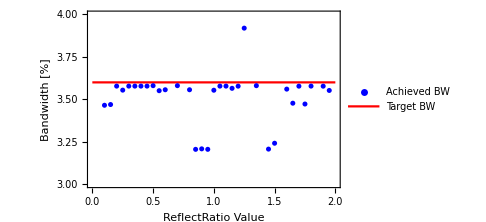

```mathematica
ReflectRatioPlot=ListPlot[{Transpose[{ReflectRatioTest⟦All,1⟧,Transpose[RRAchBW]⟦1⟧}],RRTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"ReflectRatio Value","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.18}],PlotRange->{{0,2},{3,4}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{ReflectRatioTest⟦All,1⟧,Transpose[RRAchBW]⟦1⟧}]>>"RMSFEBE_ReflectRatio.txt";
```

## ExpandRatio Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
ExpandRatioTest=Table[{ER,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"ExpandRatio"->ER},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{ER,0.1,3,0.1}];
```

```mathematica
ERAchBW=Table[{(100*rmsBandwidth[Ee,λ,ExpandRatioTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ExpandRatioTest⟦i,2,2,2,2,2⟧,ExpandRatioTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[ExpandRatioTest⟦All,1⟧]}];
```

```mathematica
ERTarBW={{0,RMSBW*100},{2,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

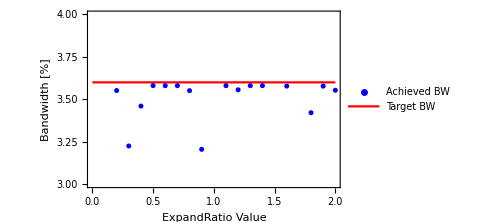

```mathematica
ExpandRatioPlot=ListPlot[{Transpose[{ExpandRatioTest⟦All,1⟧,Transpose[ERAchBW]⟦1⟧}],ERTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"ExpandRatio Value","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.8}],PlotRange->{{0,2},{3,4}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{ExpandRatioTest⟦All,1⟧,Transpose[ERAchBW]⟦1⟧}]>>"RMSFEBE_ExpandRatio.txt";
```

## ContractRatio Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
ContractRatioTest=Table[{CR,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"ContractRatio"->CR},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{CR,0.2,1,0.05}];
```

```mathematica
CRAchBW=Table[{(100*rmsBandwidth[Ee,λ,ContractRatioTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ContractRatioTest⟦i,2,2,2,2,2⟧,ContractRatioTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[ContractRatioTest⟦All,1⟧]}];
```

```mathematica
CRTarBW={{0,RMSBW*100},{2,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

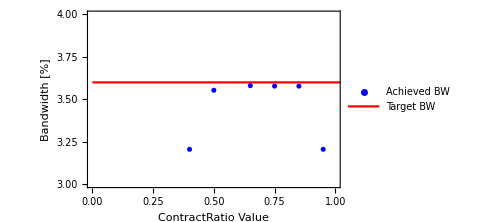

```mathematica
ContractRatioPlot=ListPlot[{Transpose[{ContractRatioTest⟦All,1⟧,Transpose[CRAchBW]⟦1⟧}],CRTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"ContractRatio Value","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.8}],PlotRange->{{0,1},{3,4}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{ContractRatioTest⟦All,1⟧,Transpose[CRAchBW]⟦1⟧}]>>"RMSFEBE_ContractRatio.txt";
```

## ShrinkRatio Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
ShrinkRatioTest=Table[{SR,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"ShrinkRatio"->SR},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{SR,0.1,1,0.05}];
```

```mathematica
SRAchBW=Table[{(100*rmsBandwidth[Ee,λ,ShrinkRatioTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ShrinkRatioTest⟦i,2,2,2,2,2⟧,ShrinkRatioTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[ShrinkRatioTest⟦All,1⟧]}];
```

```mathematica
SRTarBW={{0,RMSBW*100},{2,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

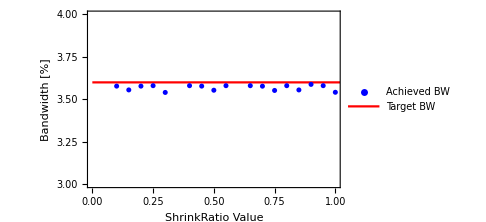

```mathematica
ShrinkRatioPlot=ListPlot[{Transpose[{ShrinkRatioTest⟦All,1⟧,Transpose[SRAchBW]⟦1⟧}],SRTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"ShrinkRatio Value","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.8}],PlotRange->{{0,1},{3,4}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{ShrinkRatioTest⟦All,1⟧,Transpose[SRAchBW]⟦1⟧}]>>"RMSFEBE_ShrinkRatio.txt";
```

## MaxIterations Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
NKERNELS=20;
```

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvi,NIntegrate::inumr,NMaximize::nosat]];
```

```mathematica
DistributeDefinitions[Fcol,trialcase,NMTOL,RMSBW,rmsBandwidth];
```

```mathematica
MaxIterationsTest=ParallelTable[{Nit,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL},MaxIterations->Nit,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{Nit,50,2500,50}];
```

```mathematica
CloseKernels[];
```

```mathematica
MITAchBW=Table[{(100*rmsBandwidth[Ee,λ,MaxIterationsTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,MaxIterationsTest⟦i,2,2,2,2,2⟧,MaxIterationsTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[MaxIterationsTest⟦All,1⟧]}];
```

```mathematica
MITTarBW={{0,RMSBW*100},{2500,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

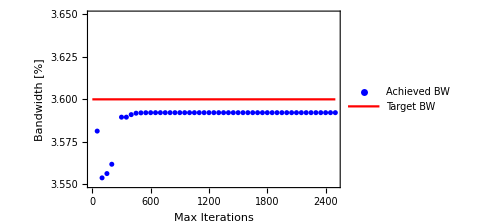

```mathematica
MaxIterationsPlot=ListPlot[{Transpose[{MaxIterationsTest⟦All,1⟧,Transpose[MITAchBW]⟦1⟧}],MITTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"Max Iterations","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.8}],PlotRange->{{0,2500},{3.55,3.65}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{MaxIterationsTest⟦All,1⟧,Transpose[MITAchBW]⟦1⟧}]>>"RMSFEBE_MaxIterations.txt";
```

## Tolerance Parameter -[NEEDS WORK]

```mathematica
RMSBW=3.6/100;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
ToleranceTest=Table[{10^NTOL,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->10^NTOL},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{NTOL,-1,-15,-1}];
```

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 1/10000: {0.036-√(475010. (Times[«2»]+Times[«2»])+(4.81333×10^9 θcol^4)/Plus[«2»]^2+(6.43805×10^-11)/Plus[«2»]^2+(0.00101442 Plus[«2»]^2)/Plus[«2»]^2)==0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 1/100000: {0.036-√(475010. (Times[«2»]+Times[«2»])+(4.81333×10^9 θcol^4)/Plus[«2»]^2+(6.43805×10^-11)/Plus[«2»]^2+(0.00101442 Plus[«2»]^2)/Plus[«2»]^2)==0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 1/1000000: {0.036-√(475010. (Times[«2»]+Times[«2»])+(4.81333×10^9 θcol^4)/Plus[«2»]^2+(6.43805×10^-11)/Plus[«2»]^2+(0.00101442 Plus[«2»]^2)/Plus[«2»]^2)==0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

```mathematica
TOLAchBW=Table[{(100*rmsBandwidth[Ee,λ,ToleranceTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ToleranceTest⟦i,2,2,2,2,2⟧,ToleranceTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[ToleranceTest⟦All,1⟧]}];
```

```mathematica
TOLTarBW={{10^-1,RMSBW*100},{10^-15,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
(*HOW TO PLOT*)
```

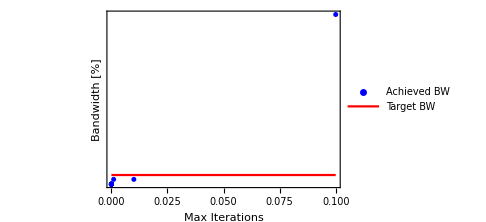

```mathematica
MaxIterationsPlot=ListLogPlot[{Transpose[{ToleranceTest⟦All,1⟧,Transpose[TOLAchBW]⟦1⟧}],TOLTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"Max Iterations","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.8}],PlotRange->{{10^-1,10^-15},{3,4}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{MaxIterationsTest⟦All,1⟧,Transpose[MITAchBW]⟦1⟧}]>>"RMSFEBE_MaxIterations.txt";
```

Differental Evolution

## MaxIterations Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
NKERNELS=20;
```

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvi,NIntegrate::inumr,NMaximize::nosat]];
```

```mathematica
DistributeDefinitions[Fcol,trialcase,NMTOL,RMSBW,rmsBandwidth];
```

```mathematica
MaxIterationsTest=ParallelTable[{Nit,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"DifferentialEvolution","Tolerance"->NMTOL},MaxIterations->Nit,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{Nit,50,1000,50}];
```

```mathematica
CloseKernels[];
```

```mathematica
MITAchBW=Table[{(100*rmsBandwidth[Ee,λ,MaxIterationsTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,MaxIterationsTest⟦i,2,2,2,2,2⟧,MaxIterationsTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[MaxIterationsTest⟦All,1⟧]}];
```

```mathematica
MITTarBW={{0,RMSBW*100},{1000,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

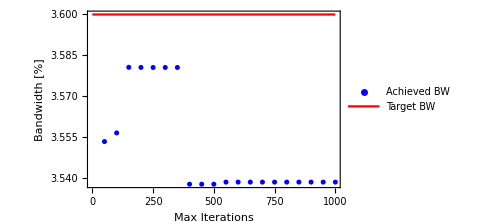

```mathematica
MaxIterationsPlot=ListPlot[{Transpose[{MaxIterationsTest⟦All,1⟧,Transpose[MITAchBW]⟦1⟧}],MITTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"Max Iterations","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.22,0.8}],PlotRange->Full,ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{MaxIterationsTest⟦All,1⟧,Transpose[MITAchBW]⟦1⟧}]>>"RMSFEBE_MaxIterations_DE.txt";
```

## CrossProbability Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
NKERNELS=20;
```

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvi,NIntegrate::inumr,NMaximize::nosat]];
```

```mathematica
DistributeDefinitions[Fcol,trialcase,NMTOL,RMSBW,rmsBandwidth];
```

```mathematica
CrossProbabilityTest=ParallelTable[{CP,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"DifferentialEvolution","Tolerance"->NMTOL,"CrossProbability"->CP},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{CP,0.01,1,0.01}];
```

```mathematica
CloseKernels[];
```

```mathematica
CPAchBW=Table[{(100*rmsBandwidth[Ee,λ,CrossProbabilityTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,CrossProbabilityTest⟦i,2,2,2,2,2⟧,CrossProbabilityTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[CrossProbabilityTest⟦All,1⟧]}];
```

```mathematica
CPTarBW={{0,RMSBW*100},{1,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

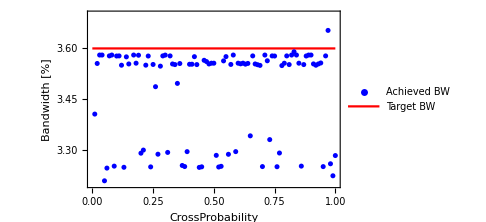

```mathematica
CrossProbabilityPlot=ListPlot[{Transpose[{CrossProbabilityTest⟦All,1⟧,Transpose[CPAchBW]⟦1⟧}],CPTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"CrossProbability","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.5}],PlotRange->{{0,1},{3.2,3.7}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{CrossProbabilityTest⟦All,1⟧,Transpose[CPAchBW]⟦1⟧}]>>"RMSFEBE_CrossProbability_DE.txt";
```

## ScalingFactor Parameter

```mathematica
RMSBW=3.6/100;
NMTOL=10^-12;
NKERNELS=20;
```

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvi,NIntegrate::inumr,NMaximize::nosat]];
```

```mathematica
DistributeDefinitions[Fcol,trialcase,NMTOL,RMSBW,rmsBandwidth];
```

```mathematica
ScalingFactorTest=ParallelTable[{SF,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"DifferentialEvolution","Tolerance"->NMTOL,"ScalingFactor"->SF},MaxIterations->100,WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15]//AbsoluteTiming},{SF,0.01,2,0.01}];
```

```mathematica
CloseKernels[];
```

```mathematica
SFAchBW=Table[{(100*rmsBandwidth[Ee,λ,ScalingFactorTest⟦i,2,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ScalingFactorTest⟦i,2,2,2,2,2⟧,ScalingFactorTest⟦i,2,2,2,3,2⟧]/.trialcase)},{i,1,Length[ScalingFactorTest⟦All,1⟧]}];
```

```mathematica
SFTarBW={{0,RMSBW*100},{2,RMSBW*100}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

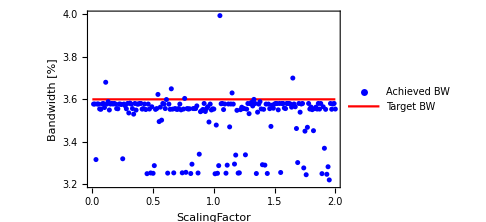

```mathematica
ScalingFactorPlot=ListPlot[{Transpose[{ScalingFactorTest⟦All,1⟧,Transpose[SFAchBW]⟦1⟧}],SFTarBW},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Red},Frame->True,FrameLabel->{"ScalingFactor","Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Achieved BW","Target BW"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.7}],PlotRange->{{0,2},{3.2,4}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/FEBE"];
Transpose[{ScalingFactorTest⟦All,1⟧,Transpose[SFAchBW]⟦1⟧}]>>"RMSFEBE_ScalingFactor_DE.txt";
```

## rms BW Single Point Optimisation (2D Simplex/NelderMead)

## Setup of Optimisation Parameters

```mathematica
RMSBW=0.5/100;
NMTOL=10^-6;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
singoptvalrms=NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-4,βIPx>10^-3,βIPy>10^-3},{θcol,βIPx,βIPy},Method->{"SimulatedAnnealing","Tolerance"->NMTOL},MaxIterations->100]//AbsoluteTiming;
```

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 1/1000000: {0.005-√(4980.24 (Times[«2»]+Times[«2»])+(517665. θcol^4)/Plus[«2»]^2+(3.60164×10^-7)/Plus[«2»]^2+(2.17156×10^-7 Plus[«2»]^2)/Plus[«2»]^2)==0}.

```mathematica
RMSoptGrid=Grid[{{"RMS Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"RMS Target Bandwidth","(ΔE_γ/E_γ)_RMS",RMSBW*100,"%"},{"RMS Achieved Bandwidth","(ΔE_γ/E_γ)_RMS",(100*rmsBandwidth[Ee,λ,singoptvalrms⟦2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,singoptvalrms⟦2,2,2,2⟧,singoptvalrms⟦2,2,3,2⟧]/.trialcase),"%"},{"Collimation Angle","θ_col",singoptvalrms⟦2,2,1,2⟧/mrad//N,"mrad"},{"β_x-function at the IP","(β^*)_x",singoptvalrms⟦2,2,2,2⟧,"m"},{"β_y-function at the IP","(β^*)_y",singoptvalrms⟦2,2,3,2⟧,"m"},{"Collimated Flux","F_col",singoptvalrms⟦2,1⟧,"ph/s"},{"Simulation Time","t_sim",singoptvalrms⟦1⟧,"s"}},Dividers->{{True,True,True,True,True},{True,True,True,False,True,False,False,True,True,True}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1.11781 | %
Collimation Angle | θ_col | 2.64244 | mrad
β_x-function at the IP | (β^*)_x | 0.00100002 | m
β_y-function at the IP | (β^*)_y | 0.001 | m
Collimated Flux | F_col | 1.19384×10^8 | ph/s
Simulation Time | t_sim | 107.972 | s

```mathematica
Options[NMaximize]
```

{AccuracyGoal→Automatic,EvaluationMonitor→None,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Single_Point/2D_NRB_Simplex"];
RMSoptGrid>>"RMSCASEB-2BW-Grid.txt";
singoptvalrms>>"RMSCASEB-2BW-Data.txt";
```

Data saved in particular accelerator’s folder. Naming Convention: <RMS | FWHM><ACC><Beam KE>-<BW as %>BW-<Grid | Data>.txt

## Parameter Space Investigation

```mathematica
{sol,pts}=Reap[NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"RandomSeed"->58},EvaluationMonitor:>Sow[{θcol/mrad,βIPx,βIPy}]]];
```

```mathematica
θcolβxsol={{sol⟦2,1,2⟧/mrad,sol⟦2,2,2⟧}};
θcolβysol={{sol⟦2,1,2⟧/mrad,sol⟦2,3,2⟧}};
βxβysol={{sol⟦2,2,2⟧,sol⟦2,3,2⟧}};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
NMθcolβxplot=ListPlot[{Partition[Riffle[pts⟦1,All,1⟧,pts⟦1,All,2⟧],2],θcolβxsol},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotStyle->{Blue,{Red,PointSize[0.02]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Trials","Solution"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.85,0.8}],PlotRange->{{0,1},{0,4}},ImageSize->Medium];
```

```mathematica
NMθcolβyplot=ListPlot[{Partition[Riffle[pts⟦1,All,1⟧,pts⟦1,All,3⟧],2],θcolβysol},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotStyle->{Blue,{Red,PointSize[0.02]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Trials","Solution"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.85,0.8}],PlotRange->{{0,1},{0,1}},ImageSize->Medium];
```

```mathematica
NMβxβyplot=ListPlot[{Partition[Riffle[pts⟦1,All,2⟧,pts⟦1,All,3⟧],2],βxβysol},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotStyle->{Blue,{Red,PointSize[0.02]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Trials","Solution"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.2}],PlotRange->{{0,4},{0,1}},ImageSize->Medium];
```

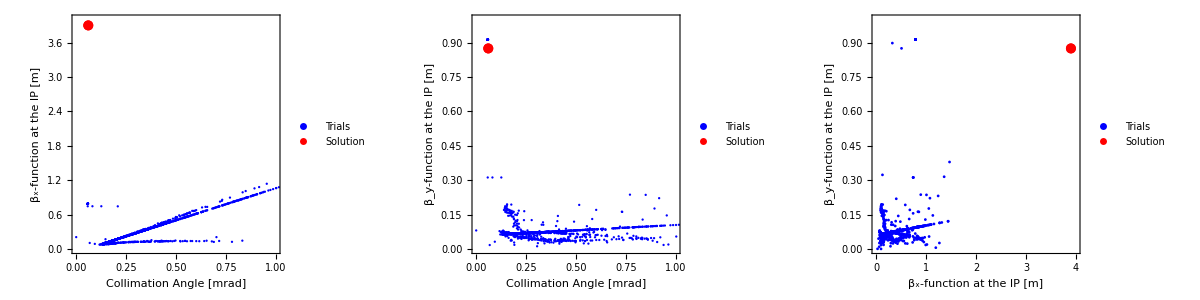

```mathematica
Grid[{{NMθcolβxplot,NMθcolβyplot,NMβxβyplot}}]
```

## Multi-Seed, Single Bandwidth

```mathematica
NMTOL=10^-7;
NKERNELS=30;
```

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
DistributeDefinitions[Fcol,rmsBandwidth,NMTOL,RMSBW,RACHG,σ,trialcase];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::nlim,NIntegrate::inumr,NIntegrate::ncvi,NMaximize::nosat,Power::infy,Infinity::indet,NIntegrate::inumri,NMaximize::nnum]];
```

```mathematica
multiseedsingoptvalrms=ParallelTable[{nseed,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"RandomSeed"->nseed}]},{nseed,1,50}]//AbsoluteTiming;
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
achievedrmsBW=Table[(rmsBandwidth[Ee,λ,multiseedsingoptvalrms⟦2,i,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,multiseedsingoptvalrms⟦2,i,2,2,2,2⟧,multiseedsingoptvalrms⟦2,i,2,2,3,2⟧]/.trialcase)*100,{i,1,Length[multiseedsingoptvalrms⟦2⟧]}];
```

```mathematica
multiseedsingoptvalrms={multiseedsingoptvalrms⟦1⟧,Table[Insert[multiseedsingoptvalrms⟦2,i⟧,((RMSBW*100)-achievedrmsBW⟦i⟧),3],{i,1,Length[achievedrmsBW]}]};
```

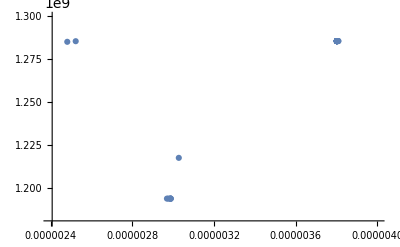

```mathematica
ListPlot[Partition[Riffle[Abs[multiseedsingoptvalrms⟦2,All,3⟧],multiseedsingoptvalrms⟦2,All,2,1⟧],2],PlotRange->{{2.4*10^-6,4*10^-6},{1.18*10^9,1.3*10^9}}]
```

## rms BW Tuning Curve Optimisation (2D Simplex/NelderMead)

## Setup of Optimisation Parameters

```mathematica
RMSBWmin=rmsMTB[ΔEe,Δλ]/.trialcase;
RMSBWmax=1/100;
RMSBWstep=0.005/100;
NMTOL=10^-7;
NKERNELS=30;
```

## rms Tuning Curve Optimisation

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
DistributeDefinitions[Fcol,rmsBandwidth,NMTOL,RMSBWmin,RMSBWmax,RMSBWstep,RACHG,σ,trialcase];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::nlim,NIntegrate::inumr,NIntegrate::ncvi,NMaximize::nosat,Power::infy,Infinity::indet,NIntegrate::inumri,NMaximize::nnum]];
```

```mathematica
tuningcurverms=ParallelTable[{rmsBW*100,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,rmsBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"SimulatedAnnealing","Tolerance"->NMTOL}]},{rmsBW,RMSBWmin,RMSBWmax,RMSBWstep}]//AbsoluteTiming;
```

```mathematica
CloseKernels[];
```

```mathematica
rmsTuningCurveData=Grid[{{"RMS Tuning Curve Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"Simulation Time","t_sim",tuningcurverms⟦1⟧/60,"min"},{"No. Sim Points","n_pts",Length[tuningcurverms⟦2⟧],""},{"Sim Time per Point","t_pts",tuningcurverms⟦1⟧/(60*Length[tuningcurverms⟦2⟧]),"min"}},Dividers->{{True,True,True,True,True},{True,True,True,False,False,True}}]
```

RMS Tuning Curve Optimisation |  |  | 
Parameter | Symbol | Value | Unit
Simulation Time | t_sim | 72.078 | min
No. Sim Points | n_pts | 185 | 
Sim Time per Point | t_pts | 0.389611 | min

## Achieved Bandwidth Calculation + Appending to data

```mathematica
achievedrmsBW=Table[(rmsBandwidth[Ee,λ,tuningcurverms⟦2,i,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,tuningcurverms⟦2,i,2,2,2,2⟧,tuningcurverms⟦2,i,2,2,3,2⟧]/.trialcase)*100,{i,1,Length[tuningcurverms⟦2⟧]}];
```

This next line appends the achieved BW values to the tuningcurverms array.

```mathematica
tuningcurverms={tuningcurverms⟦1⟧,Table[Insert[tuningcurverms⟦2,i⟧,achievedrmsBW⟦i⟧,3],{i,1,Length[achievedrmsBW]}]};
```

```mathematica
BWach[BWlin_]:=BWlin;
BWlinear=Table[{BWlin,BWach[BWlin]},{BWlin,0,1,0.01}];
```

## Drawing of RB β_x-β_y

```mathematica
βyrb[βxrb_]:=βxrb;
```

```mathematica
βxβyRB=Table[{βxrb,βyrb[βxrb]},{βxrb,0,20,0.01}];
```

## Saving Data

Data is stored in the form {total sim time,{target BW, {theta→val,β_x→val, β_y→val},achieved BW}}. The total simulation time is obviously one value. tuningcurverms⟦2⟧ is where the actual data is.

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/Thesis"];
tuningcurverms>>"CaseCsimplexRMS_SA.txt";
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
FBWplot=ListPlot[Partition[Riffle[tuningcurverms⟦2,All,3⟧,tuningcurverms⟦2,All,2,1⟧],2],PlotStyle->{PointSize[0.015],Black},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,1},{0,3*10^8}}];
```

```mathematica
BWachBWtarplot=ListPlot[{BWlinear,Partition[Riffle[tuningcurverms⟦2,All,1⟧,tuningcurverms⟦2,All,3⟧],2]},Joined->{True,False},PlotStyle->{Black,{PointSize[0.02],Orange}},Frame->True,FrameLabel->{"rms Target Bandwidth [%]","rms Achieved Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,1},{0,10}}];
```

```mathematica
θcolβxplot=ListPlot[Partition[Riffle[tuningcurverms⟦2,All,2,2,1,2⟧/mrad,tuningcurverms⟦2,All,2,2,2,2⟧],2],PlotStyle->{PointSize[0.02],Red},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,4},{0,20}}];
```

```mathematica
θcolβyplot=ListPlot[Partition[Riffle[tuningcurverms⟦2,All,2,2,1,2⟧/mrad,tuningcurverms⟦2,All,2,2,3,2⟧],2],PlotStyle->{PointSize[0.02],Blue},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,4},{0,20}}];
```

```mathematica
βxβyplot=ListPlot[{Partition[Riffle[tuningcurverms⟦2,All,2,2,2,2⟧,tuningcurverms⟦2,All,2,2,3,2⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.02],Green},Black},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB Simplex","RB"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

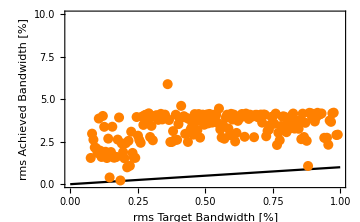

```mathematica
BWachBWtarplot
```

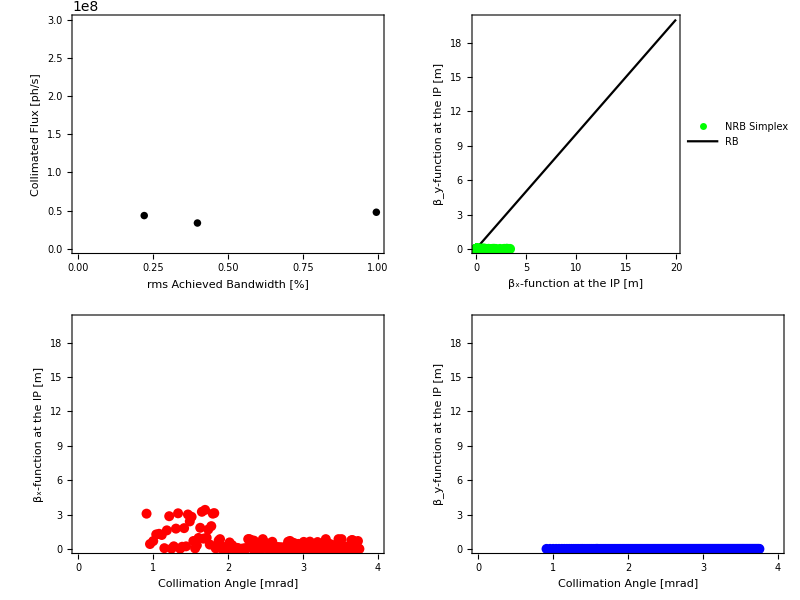

```mathematica
simplexRMSplots=Grid[{{FBWplot,βxβyplot},{θcolβxplot,θcolβyplot}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/Thesis"];
Export["Case_C_simplex_Tuning_Curves.pdf",simplexRMSplots];
```

## Crab Crossing rms BW Single Point Optimisation (2D Simplex/NelderMead)

## Setup of Optimisation Parameters

```mathematica
RMSBW=0.5/100;
NMTOL=10^-7;
```

```mathematica
Off[NIntegrate::ncvi];
```

```mathematica
CCsingoptvalrms=NMaximize[{CCFcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL,"RandomSeed"->58}]//AbsoluteTiming;
```

```mathematica
CCRMSoptGrid=Grid[{{"RMS Optimisation (Crab Crossing)",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"RMS Target Bandwidth","(ΔE_γ/E_γ)_RMS",RMSBW*100,"%"},{"RMS Achieved Bandwidth","(ΔE_γ/E_γ)_RMS",(100*rmsBandwidth[Ee,λ,CCsingoptvalrms⟦2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,CCsingoptvalrms⟦2,2,2,2⟧,CCsingoptvalrms⟦2,2,3,2⟧]/.trialcase),"%"},{"Collimation Angle","θ_col",CCsingoptvalrms⟦2,2,1,2⟧/mrad//N,"mrad"},{"β_x-function at the IP","(β^*)_x",CCsingoptvalrms⟦2,2,2,2⟧,"m"},{"β_y-function at the IP","(β^*)_y",CCsingoptvalrms⟦2,2,3,2⟧,"m"},{"Collimated Flux","F_col",CCsingoptvalrms⟦2,1⟧,"ph/s"},{"Simulation Time","t_sim",CCsingoptvalrms⟦1⟧,"s"}},Dividers->{{True,True,True,True,True},{True,True,True,False,True,False,False,True,True,True}}]
```

RMS Optimisation (Crab Crossing) |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.500004 | %
Collimation Angle | θ_col | 0.0597531 | mrad
β_x-function at the IP | (β^*)_x | 0.917586 | m
β_y-function at the IP | (β^*)_y | 0.917587 | m
Collimated Flux | F_col | 1.11787×10^10 | ph/s
Simulation Time | t_sim | 95.3379 | s

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
CCRMSoptGrid>>"RMSDIANA1072-CC-0.5BW-Grid.txt";
CCsingoptvalrms>>"RMSDIANA1072-CC-0.5BW-Data.txt";
```

Data saved in particular accelerator’s folder. Naming Convention: <RMS | FWHM><ACC><Beam KE>-CC-<BW as %>BW-<Grid | Data>.txt

## Crab Crossing rms BW Tuning Curve Optimisation (2D Simplex/NelderMead)

## Setup of Optimisation Parameters

```mathematica
RMSBWmin=rmsMTB[ΔEe,Δλ]/.trialcase;
RMSBWmax=1/100;
RMSBWstep=0.005/100;
NMTOL=10^-7;
NKERNELS=30;
```

## rms Tuning Curve Optimisation

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
DistributeDefinitions[Fcol,rmsBandwidth,NMTOL,RMSBWmin,RMSBWmax,RMSBWstep,RACHG,σ,trialcase];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::nlim,NIntegrate::inumr,NIntegrate::ncvi,NMaximize::nosat,Power::infy,Infinity::indet,NIntegrate::inumri,NMaximize::nnum]];
```

```mathematica
CCtuningcurverms=ParallelTable[{rmsBW*100,NMaximize[{CCFcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,rmsBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL}]},{rmsBW,RMSBWmin,RMSBWmax,RMSBWstep}]//AbsoluteTiming;
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
CloseKernels[];
```

```mathematica
CCrmsTuningCurveData=Grid[{{"RMS Tuning Curve Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"Simulation Time","t_sim",CCtuningcurverms⟦1⟧/60,"min"},{"No. Sim Points","n_pts",Length[CCtuningcurverms⟦2⟧],""},{"Sim Time per Point","t_pts",CCtuningcurverms⟦1⟧/(60*Length[CCtuningcurverms⟦2⟧]),"min"}},Dividers->{{True,True,True,True,True},{True,True,True,False,False,True}}]
```

RMS Tuning Curve Optimisation |  |  | 
Parameter | Symbol | Value | Unit
Simulation Time | t_sim | 85.1325 | min
No. Sim Points | n_pts | 187 | 
Sim Time per Point | t_pts | 0.455254 | min

## Achieved Bandwidth Calculation + Appending to data

```mathematica
CCachievedrmsBW=Table[(rmsBandwidth[Ee,λ,CCtuningcurverms⟦2,i,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,CCtuningcurverms⟦2,i,2,2,2,2⟧,CCtuningcurverms⟦2,i,2,2,3,2⟧]/.trialcase)*100,{i,1,Length[CCtuningcurverms⟦2⟧]}];
```

This next line appends the achieved BW values to the tuningcurverms array.

```mathematica
CCtuningcurverms={CCtuningcurverms⟦1⟧,Table[Insert[CCtuningcurverms⟦2,i⟧,CCachievedrmsBW⟦i⟧,3],{i,1,Length[CCachievedrmsBW]}]};
```

```mathematica
BWach[BWlin_]:=BWlin;
BWlinear=Table[{BWlin,BWach[BWlin]},{BWlin,0,1,0.01}];
```

## Drawing of RB β_x-β_y

```mathematica
βyrb[βxrb_]:=βxrb;
```

```mathematica
βxβyRB=Table[{βxrb,βyrb[βxrb]},{βxrb,0,20,0.01}];
```

## Saving Data

Data is stored in the form {total sim time,{target BW, {theta→val,β_x→val, β_y→val},achieved BW}}. The total simulation time is obviously one value. tuningcurverms⟦2⟧ is where the actual data is.

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
CCtuningcurverms>>"DIANA1072simplexRMSCC.txt";
CCrmsTuningCurveData>>"DIANA1072simplexRMSCC_SET.txt";
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
FBWplot=ListPlot[Partition[Riffle[CCtuningcurverms⟦2,All,3⟧,CCtuningcurverms⟦2,All,2,1⟧],2],PlotStyle->{PointSize[0.015],Black},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,1},{0,3*10^10}}];
```

```mathematica
BWachBWtarplot=ListPlot[{BWlinear,Partition[Riffle[CCtuningcurverms⟦2,All,1⟧,CCtuningcurverms⟦2,All,3⟧],2]},Joined->{True,False},PlotStyle->{Black,{PointSize[0.02],Orange}},Frame->True,FrameLabel->{"rms Target Bandwidth [%]","rms Achieved Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,1},{0,1}}];
```

```mathematica
θcolβxplot=ListPlot[Partition[Riffle[CCtuningcurverms⟦2,All,2,2,1,2⟧/mrad,CCtuningcurverms⟦2,All,2,2,2,2⟧],2],PlotStyle->{PointSize[0.02],Red},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,0.1},{0,15}}];
```

```mathematica
θcolβyplot=ListPlot[Partition[Riffle[CCtuningcurverms⟦2,All,2,2,1,2⟧/mrad,CCtuningcurverms⟦2,All,2,2,3,2⟧],2],PlotStyle->{PointSize[0.02],Blue},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium,PlotRange->{{0,0.1},{0,15}}];
```

```mathematica
βxβyplot=ListPlot[{Partition[Riffle[CCtuningcurverms⟦2,All,2,2,2,2⟧,CCtuningcurverms⟦2,All,2,2,3,2⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.02],Green},Black},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB Simplex","RB"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

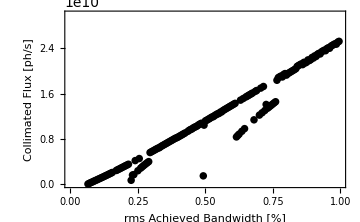
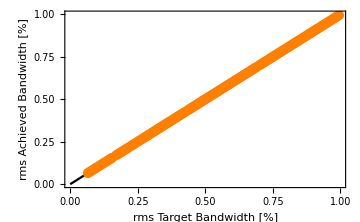
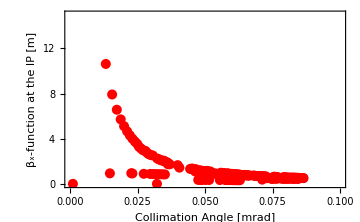
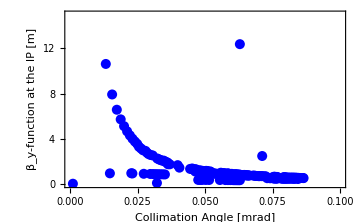
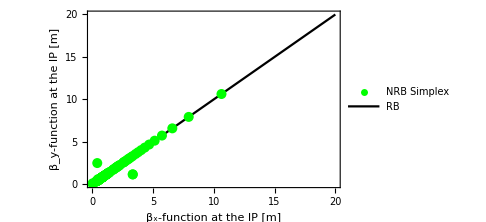
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{FBWplot,BWachBWtarplot},{θcolβxplot,θcolβyplot,βxβyplot}}]
```

## Emittance - F_col Tuning Curve (Constant Bandwidth)

Basically, grow the emittance from 0.25 mm-mrad to 1 mm-mrad symmetrically + plot points on F_col-ϵ_n space.

## Setup

```mathematica
RMSBW=0.5/100;
NMTOL=SuperMinus[10];
NKERNELS=30;
ϵnmin=0.25mm mrad;
ϵnmax=1.00 mm mrad;
ϵnstep=0.01mm mrad;
```

## Optimisation

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
DistributeDefinitions[Fcol,rmsBandwidth,NMTOL,RMSBW,RACHG,σ,trialcase,ϵnmin,ϵnmax,ϵnstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::nlim,NIntegrate::inumr,NIntegrate::ncvi,NMaximize::nosat,Power::infy,Infinity::indet,NIntegrate::inumri,NMaximize::nnum]];
```

```mathematica
ϵnFcolTCrms=ParallelTable[{ϵn/(mm mrad),NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵn,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵn,ϵn,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL}]},{ϵn,ϵnmin,ϵnmax,ϵnstep}]//AbsoluteTiming;
```

```mathematica
CloseKernels[];
```

## Results + Plotting

```mathematica
ϵnFcolTCData=Grid[{{"RMS Tuning Curve Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"Simulation Time","t_sim",ϵnFcolTCrms⟦1⟧/60,"min"},{"No. Sim Points","n_pts",Length[ϵnFcolTCrms⟦2⟧],""},{"Sim Time per Point","t_pts",ϵnFcolTCrms⟦1⟧/(60*Length[ϵnFcolTCrms⟦2⟧]),"min"}},Dividers->{{True,True,True,True,True},{True,True,True,False,False,True}}]
```

RMS Tuning Curve Optimisation |  |  | 
Parameter | Symbol | Value | Unit
Simulation Time | t_sim | 44.3652 | min
No. Sim Points | n_pts | 76 | 
Sim Time per Point | t_pts | 0.583752 | min

```mathematica
ϵnFcol=ListPlot[Partition[Riffle[ϵnFcolTCrms⟦2,All,1⟧,ϵnFcolTCrms⟦2,All,2,1⟧],2],PlotStyle->{PointSize[0.015],Red},PlotRange->{{0.25,1},{8*10^8,1.5*10^9}},Frame->True,FrameLabel->{"Normalised Emittance (sym.) [mm mrad]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

```mathematica
ϵnθcol=ListPlot[Partition[Riffle[ϵnFcolTCrms⟦2,All,1⟧,ϵnFcolTCrms⟦2,All,2,2,1,2⟧/mrad],2],PlotStyle->{PointSize[0.015],Red},PlotRange->{{0.25,1},{0.055,0.065}},Frame->True,FrameLabel->{"Normalised Emittance (sym.) [mm mrad]","Collimation Angle [mrad]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

```mathematica
ϵnβx=ListPlot[Partition[Riffle[ϵnFcolTCrms⟦2,All,1⟧,ϵnFcolTCrms⟦2,All,2,2,2,2⟧],2],PlotStyle->{PointSize[0.015],Red},PlotRange->{{0.25,1},{0,6}},Frame->True,FrameLabel->{"Normalised Emittance (sym.) [mm mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

```mathematica
ϵnβy=ListPlot[Partition[Riffle[ϵnFcolTCrms⟦2,All,1⟧,ϵnFcolTCrms⟦2,All,2,2,3,2⟧],2],PlotStyle->{PointSize[0.015],Red},PlotRange->{{0.25,1},{0.5,1.5}},Frame->True,FrameLabel->{"Normalised Emittance (sym.) [mm mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

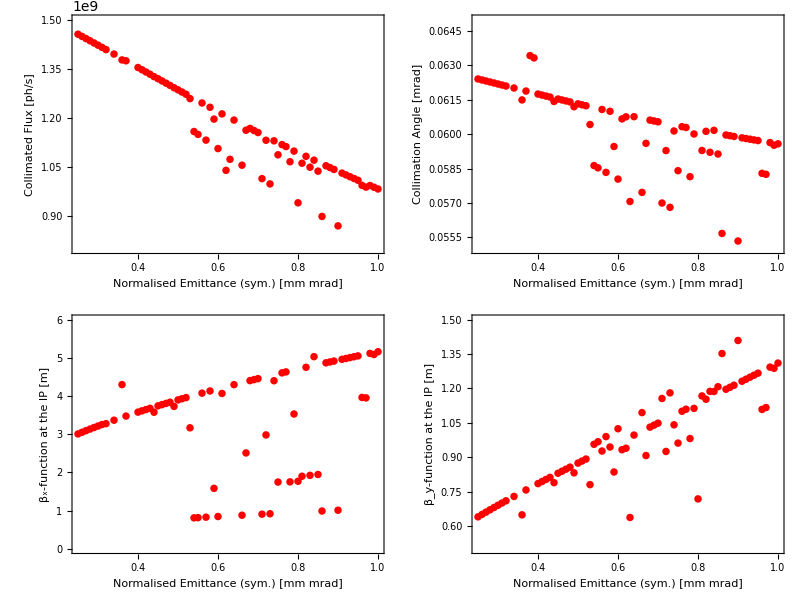

```mathematica
Grid[{{ϵnFcol,ϵnθcol},{ϵnβx,ϵnβy}}]
```

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA/Parameter Curves"];
Export["emitFcol_DIANA1072_0.5BW.png",ϵnFcol];
Export["emitFcol_DIANA1072_0.5BW.txt",ϵnFcolTCrms];
Export["emitFFcol_DIANA1072_0.5BW_simdat.txt",ϵnFcolTCData];
```

## Test Remove Shit data

```mathematica
achievedrmsBW=Table[(rmsBandwidth[Ee,λ,ϵnFcolTCrms⟦2,i,2,2,1,2⟧,ϕ,ΔEe,Δλ,ϵnx,ϵny,ϵnFcolTCrms⟦2,i,2,2,2,2⟧,ϵnFcolTCrms⟦2,i,2,2,3,2⟧]/.trialcase)*100,{i,1,Length[ϵnFcolTCrms⟦2⟧]}];
```

```mathematica
ϵnFcolTCrms={ϵnFcolTCrms⟦1⟧,Table[Insert[ϵnFcolTCrms⟦2,i⟧,((RMSBW*100)-achievedrmsBW⟦i⟧),3],{i,1,Length[achievedrmsBW]}]};
```

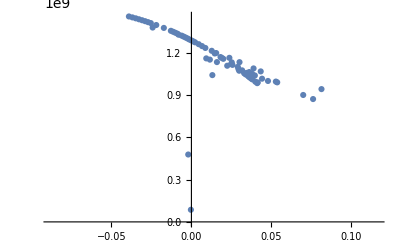

```mathematica
ListPlot[Partition[Riffle[ϵnFcolTCrms⟦2,All,3⟧,ϵnFcolTCrms⟦2,All,2,1⟧],2]]
```

## Bunch Charge - F_col Tuning Curve (Constant Bandwidth)

Basically, grow the bunch charge from 20pC to 200pC + plot points on F_col-Q space.

## Setup

```mathematica
RMSBW=0.5/100;
NMTOL=10^-7;
NKERNELS=30;
Qmin=20pC;
Qmax=200 pC;
Qstep=2.5pC;
```

## Optimisation

```mathematica
LaunchKernels[NKERNELS];
```

```mathematica
DistributeDefinitions[Fcol,rmsBandwidth,NMTOL,RMSBW,RACHG,σ,trialcase,Qmin,Qmax,Qstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::nlim,NIntegrate::inumr,NIntegrate::ncvi,NMaximize::nosat,Power::infy,Infinity::indet,NIntegrate::inumri,NMaximize::nnum]];
```

```mathematica
QFcolTCrms=ParallelTable[{Q/pC,NMaximize[{Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.trialcase,RMSBW==(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.trialcase),θcol>10^-6,βIPx>10^-6,βIPy>10^-6},{θcol,βIPx,βIPy},Method->{"NelderMead","Tolerance"->NMTOL}]},{Q,Qmin,Qmax,Qstep}]//AbsoluteTiming;
```

```mathematica
CloseKernels[];
```

## Results + Plotting

```mathematica
QFcolTCData=Grid[{{"RMS Tuning Curve Optimisation",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"Simulation Time","t_sim",QFcolTCrms⟦1⟧/60,"min"},{"No. Sim Points","n_pts",Length[QFcolTCrms⟦2⟧],""},{"Sim Time per Point","t_pts",QFcolTCrms⟦1⟧/(60*Length[QFcolTCrms⟦2⟧]),"min"}},Dividers->{{True,True,True,True,True},{True,True,True,False,False,True}}]
```

RMS Tuning Curve Optimisation |  |  | 
Parameter | Symbol | Value | Unit
Simulation Time | t_sim | 41.4819 | min
No. Sim Points | n_pts | 73 | 
Sim Time per Point | t_pts | 0.568245 | min

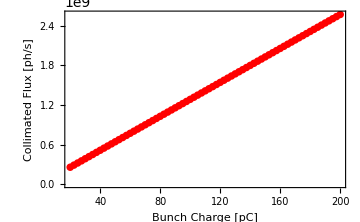

```mathematica
QFcol=ListPlot[{Partition[Riffle[QFcolTCrms⟦2,All,1⟧,QFcolTCrms⟦2,All,2,1⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.015],Red},Black},PlotRange->Full,Frame->True,FrameLabel->{"Bunch Charge [pC]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium]
```

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA/Parameter Curves"];
Export["QFcol_DIANA1072_0.5BW.png",QFcol];
Export["QFcol_DIANA1072_0.5BW.txt",QFcolTCrms];
Export["QFcol_DIANA1072_0.5BW_simdat.txt",QFcolTCData];
```

# Data Analysis

## DIANA 1072 Single BW Qualitative Comparison (Simplex NRB, Brute Force RB)

## Input Data

```mathematica
(*RB DATA*) 
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/DIANA Optimisations"];
DIANA1072RMS05RB=<<"RMS1072-0.5BW-Grid.txt";
DIANA1072RMS1RB=<<"RMS1072-1BW-Grid.txt";
```

```mathematica
(*NRB SIMPLEX DATA*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA1072RMS05NRBsimp=<<"RMSDIANA1072-0.5BW-Grid.txt";
DIANA1072RMS1NRBsimp=<<"RMSDIANA1072-1BW-Grid.txt";
```

## rms 0.5% Bandwidth Case

```mathematica
Grid[{{DIANA1072RMS05RB,DIANA1072RMS05NRBsimp}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
Collimation Angle | θ_col | 0.061 | mrad
β-function at the IP | β^* | 1.12228 | m
Collimated Flux | F_col | 1.23867×10^9 | ph/s
Simulation Time | t_sim | 28.6174 | s | RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.500004 | %
Collimation Angle | θ_col | 0.0613261 | mrad
β_x-function at the IP | (β^*)_x | 3.8987 | m
β_y-function at the IP | (β^*)_y | 0.874234 | m
Collimated Flux | F_col | 1.28931×10^9 | ph/s
Simulation Time | t_sim | 103.826 | s

```mathematica
DIANA1072RBsimNRB05=(DIANA1072RMS05NRBsimp⟦1,8,3⟧-DIANA1072RMS05RB⟦1,7,3⟧)/DIANA1072RMS05NRBsimp⟦1,8,3⟧*100
```

3.92824

## rms 1% Bandwidth Case

```mathematica
Grid[{{DIANA1072RMS1RB,DIANA1072RMS1NRBsimp}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.0879 | mrad
β-function at the IP | β^* | 0.662651 | m
Collimated Flux | F_col | 2.65718×10^9 | ph/s
Simulation Time | t_sim | 32.3627 | s | RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.0882406 | mrad
β_x-function at the IP | (β^*)_x | 2.38678 | m
β_y-function at the IP | (β^*)_y | 0.51783 | m
Collimated Flux | F_col | 2.72978×10^9 | ph/s
Simulation Time | t_sim | 101.258 | s

```mathematica
DIANA1072RBsimNRB1=(DIANA1072RMS1NRBsimp⟦1,8,3⟧-DIANA1072RMS1RB⟦1,7,3⟧)/DIANA1072RMS1NRBsimp⟦1,8,3⟧*100
```

2.65965

## DIANA 1072 Tuning Curve Comparison (Simplex NRB, Brute Force RB)

## Input Data

```mathematica
(*SIMPLEX NRB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA1072SNRB=<<"DIANA1072simplexRMS.txt";
(*BRUTE FORCE RB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA1072BFRB=<<"DIANA1072optRMS.txt";
```

## Plots

```mathematica
DIANA1072FBWsimpRB=ListPlot[{Partition[Riffle[DIANA1072BFRB⟦All,1⟧,DIANA1072BFRB⟦All,4⟧],2],Partition[Riffle[DIANA1072SNRB⟦2,All,3⟧,DIANA1072SNRB⟦2,All,2,1⟧],2]},Joined->{True,False},PlotStyle->{Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,3*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβxsimpRB=ListPlot[{Partition[Riffle[DIANA1072BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2],Partition[Riffle[DIANA1072SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA1072SNRB⟦2,All,2,2,2,2⟧],2]},Joined->{True,False},PlotStyle->{Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,15}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβysimpRB=ListPlot[{Partition[Riffle[DIANA1072BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2],Partition[Riffle[DIANA1072SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA1072SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{True,False},PlotStyle->{Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,12}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβysimpRB=ListPlot[{βxβyRB,Partition[Riffle[DIANA1072SNRB⟦2,All,2,2,2,2⟧,DIANA1072SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{True,False},PlotStyle->{Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

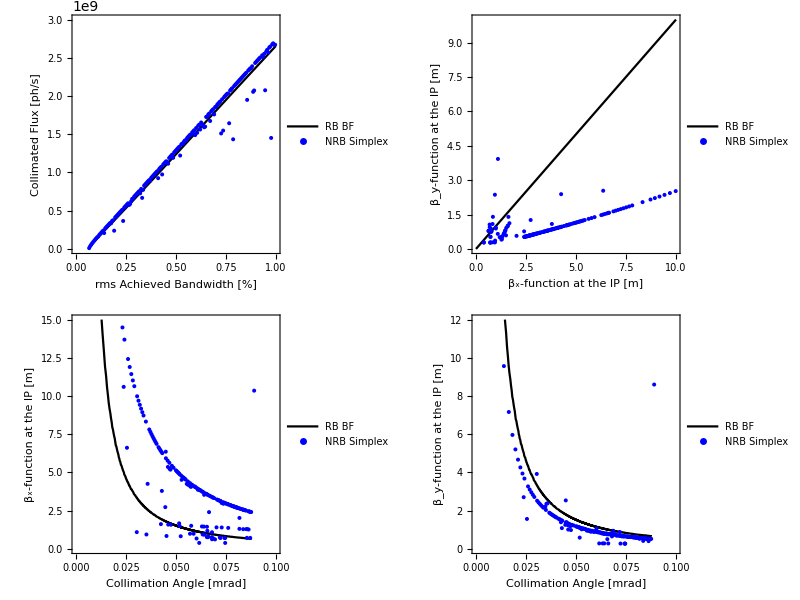

```mathematica
Grid[{{DIANA1072FBWsimpRB,DIANA1072βxβysimpRB},{DIANA1072θcolβxsimpRB,DIANA1072θcolβysimpRB}}]
```

## DIANA 1072 Tuning Curve Comparison (GA NRB, Simplex NRB, Brute Force RB)

## Input Data

```mathematica
(*GA NRB*)
DIANA1072GANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA1072_pareto.200","Table"];
(*SIMPLEX NRB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA1072SNRB=<<"DIANA1072simplexRMS.txt";
(*BRUTE FORCE RB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA1072BFRB=<<"DIANA1072optRMS.txt";
```

## Plots

```mathematica
DIANA1072FBWcomp=ListPlot[{Partition[Riffle[DIANA1072GANRB⟦All,2⟧,-DIANA1072GANRB⟦All,3⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,1⟧,DIANA1072BFRB⟦All,4⟧],2],Partition[Riffle[DIANA1072SNRB⟦2,All,3⟧,DIANA1072SNRB⟦2,All,2,1⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,3*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβxcomp=ListPlot[{Partition[Riffle[DIANA1072GANRB⟦All,4⟧,DIANA1072GANRB⟦All,5⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2],Partition[Riffle[DIANA1072SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA1072SNRB⟦2,All,2,2,2,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβycomp=ListPlot[{Partition[Riffle[DIANA1072GANRB⟦All,4⟧,DIANA1072GANRB⟦All,6⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2],Partition[Riffle[DIANA1072SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA1072SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβycomp=ListPlot[{Partition[Riffle[DIANA1072GANRB⟦All,5⟧,DIANA1072GANRB⟦All,6⟧],2],βxβyRB,Partition[Riffle[DIANA1072SNRB⟦2,All,2,2,2,2⟧,DIANA1072SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

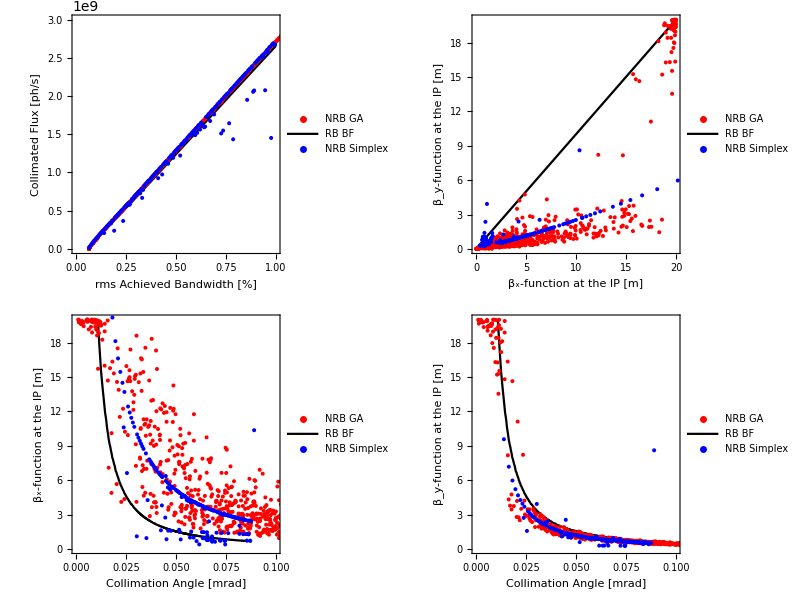

```mathematica
DIANA1072fullcomp=Grid[{{DIANA1072FBWcomp,DIANA1072βxβycomp},{DIANA1072θcolβxcomp,DIANA1072θcolβycomp}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAcomp"];
Export["DIANA1072fullcomp.png",DIANA1072fullcomp];
Export["DIANA1072fullcomp.pdf",DIANA1072fullcomp];
```

## DIANA 717 Tuning Curve Comparison (GA NRB, Simplex NRB, Brute Force RB)

## Input Data

```mathematica
(*GA NRB*)
DIANA717GANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA717_pareto.200","Table"];
(*SIMPLEX NRB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA717SNRB=<<"DIANA717simplexRMS.txt";
(*BRUTE FORCE RB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA717BFRB=<<"DIANA717optRMS.txt";
```

## Plots

```mathematica
DIANA717FBWcomp=ListPlot[{Partition[Riffle[DIANA717GANRB⟦All,2⟧,-DIANA717GANRB⟦All,3⟧],2],Partition[Riffle[DIANA717BFRB⟦All,1⟧,DIANA717BFRB⟦All,4⟧],2],Partition[Riffle[DIANA717SNRB⟦2,All,3⟧,DIANA717SNRB⟦2,All,2,1⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,3*10^9}},ImageSize->Medium];
```

```mathematica
DIANA717θcolβxcomp=ListPlot[{Partition[Riffle[DIANA717GANRB⟦All,4⟧,DIANA717GANRB⟦All,5⟧],2],Partition[Riffle[DIANA717BFRB⟦All,2⟧,DIANA717BFRB⟦All,3⟧],2],Partition[Riffle[DIANA717SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA717SNRB⟦2,All,2,2,2,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.15},{0,20}},ImageSize->Medium];
```

```mathematica
DIANA717θcolβycomp=ListPlot[{Partition[Riffle[DIANA717GANRB⟦All,4⟧,DIANA717GANRB⟦All,6⟧],2],Partition[Riffle[DIANA717BFRB⟦All,2⟧,DIANA717BFRB⟦All,3⟧],2],Partition[Riffle[DIANA717SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA717SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.15},{0,20}},ImageSize->Medium];
```

```mathematica
DIANA717βxβycomp=ListPlot[{Partition[Riffle[DIANA717GANRB⟦All,5⟧,DIANA717GANRB⟦All,6⟧],2],βxβyRB,Partition[Riffle[DIANA717SNRB⟦2,All,2,2,2,2⟧,DIANA717SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

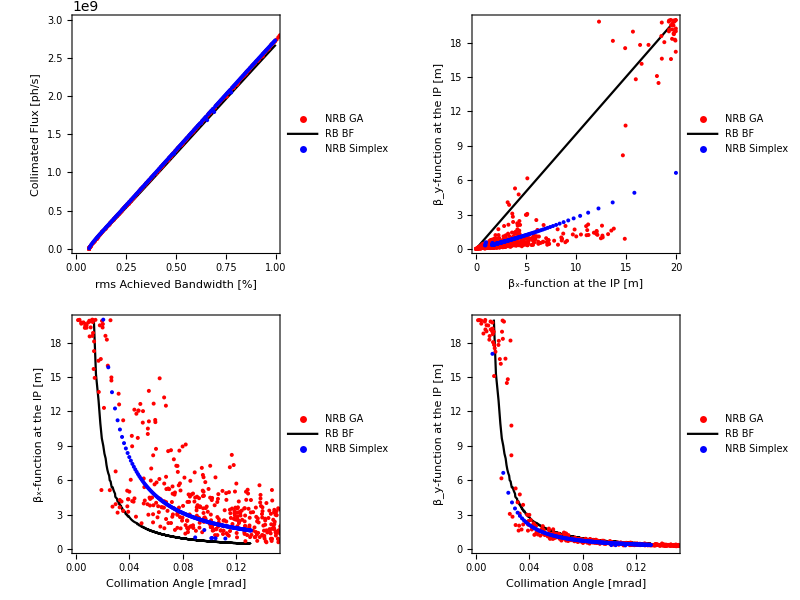

```mathematica
DIANA717fullcomp=Grid[{{DIANA717FBWcomp,DIANA717βxβycomp},{DIANA717θcolβxcomp,DIANA717θcolβycomp}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAcomp"];
Export["DIANA717fullcomp.png",DIANA717fullcomp];
Export["DIANA717fullcomp.pdf",DIANA717fullcomp];
```

## DIANA 362 Tuning Curve Comparison (GA NRB, Simplex NRB, Brute Force RB)

## Input Data

```mathematica
(*GA NRB*)
DIANA362GANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA362_pareto.200","Table"];
(*SIMPLEX NRB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA362SNRB=<<"DIANA362simplexRMS.txt";
(*BRUTE FORCE RB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA362BFRB=<<"DIANA362optRMS.txt";
```

## Plots

```mathematica
DIANA362FBWcomp=ListPlot[{Partition[Riffle[DIANA362GANRB⟦All,2⟧,-DIANA362GANRB⟦All,3⟧],2],Partition[Riffle[DIANA362BFRB⟦All,1⟧,DIANA362BFRB⟦All,4⟧],2],Partition[Riffle[DIANA362SNRB⟦2,All,3⟧,DIANA362SNRB⟦2,All,2,1⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,3*10^9}},ImageSize->Medium];
```

```mathematica
DIANA362θcolβxcomp=ListPlot[{Partition[Riffle[DIANA362GANRB⟦All,4⟧,DIANA362GANRB⟦All,5⟧],2],Partition[Riffle[DIANA362BFRB⟦All,2⟧,DIANA362BFRB⟦All,3⟧],2],Partition[Riffle[DIANA362SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA362SNRB⟦2,All,2,2,2,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.2},{0,20}},ImageSize->Medium];
```

```mathematica
DIANA362θcolβycomp=ListPlot[{Partition[Riffle[DIANA362GANRB⟦All,4⟧,DIANA362GANRB⟦All,6⟧],2],Partition[Riffle[DIANA362BFRB⟦All,2⟧,DIANA362BFRB⟦All,3⟧],2],Partition[Riffle[DIANA362SNRB⟦2,All,2,2,1,2⟧/mrad,DIANA362SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.2},{0,20}},ImageSize->Medium];
```

```mathematica
DIANA362βxβycomp=ListPlot[{Partition[Riffle[DIANA362GANRB⟦All,5⟧,DIANA362GANRB⟦All,6⟧],2],βxβyRB,Partition[Riffle[DIANA362SNRB⟦2,All,2,2,2,2⟧,DIANA362SNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

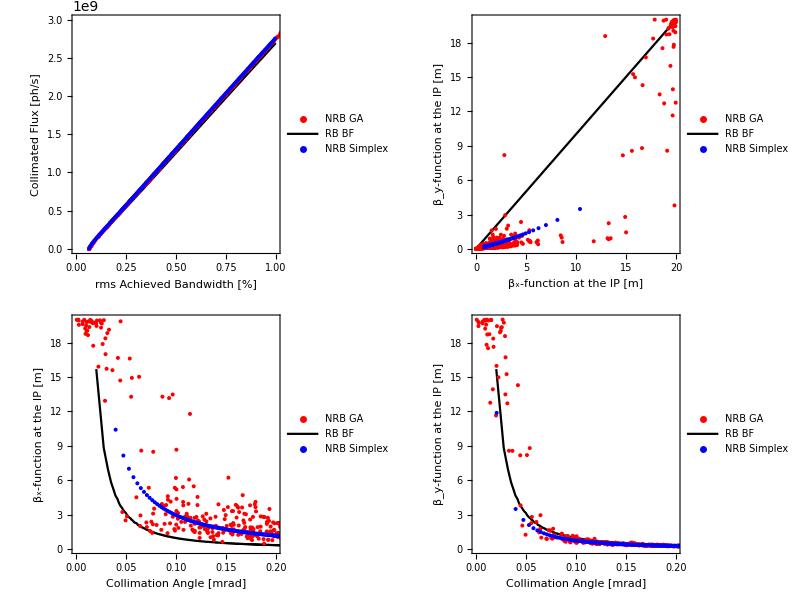

```mathematica
DIANA362fullcomp=Grid[{{DIANA362FBWcomp,DIANA362βxβycomp},{DIANA362θcolβxcomp,DIANA362θcolβycomp}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAcomp"];
Export["DIANA362fullcomp.png",DIANA362fullcomp];
Export["DIANA362fullcomp.pdf",DIANA362fullcomp];
```

## DIANA 1D RB Plots

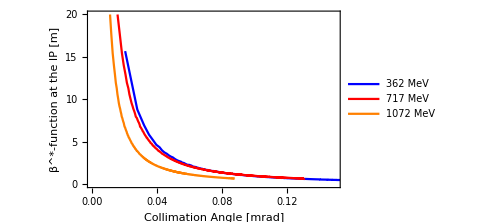

```mathematica
DIANARBβθ=ListLinePlot[{Partition[Riffle[DIANA362BFRB⟦All,2⟧,DIANA362BFRB⟦All,3⟧],2],Partition[Riffle[DIANA717BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2]},PlotStyle->{Blue,Red,Orange},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β^*-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"362 MeV","717 MeV","1072 MeV"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.75}],PlotRange->{{0,0.15},{0,20}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAcomp"];
Export["DIANARBbetathetaenergycomp.png",DIANARBβθ];
Export["DIANARBbetathetaenergycomp.pdf",DIANARBβθ];
```

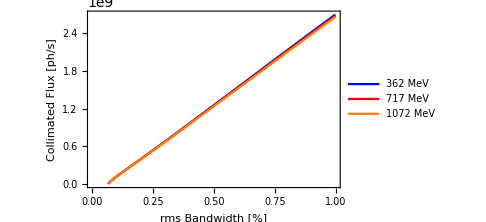

```mathematica
DIANARBFBW=ListLinePlot[{Partition[Riffle[DIANA362BFRB⟦All,1⟧,DIANA362BFRB⟦All,4⟧],2],Partition[Riffle[DIANA717BFRB⟦All,1⟧,DIANA717BFRB⟦All,4⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,1⟧,DIANA1072BFRB⟦All,4⟧],2]},PlotStyle->{Blue,Red,Orange},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"362 MeV","717 MeV","1072 MeV"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.25}],ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAcomp"];
Export["DIANARBFBWenergycomp.png",DIANARBFBW];
Export["DIANARBFBWenergycomp.pdf",DIANARBFBW];
```

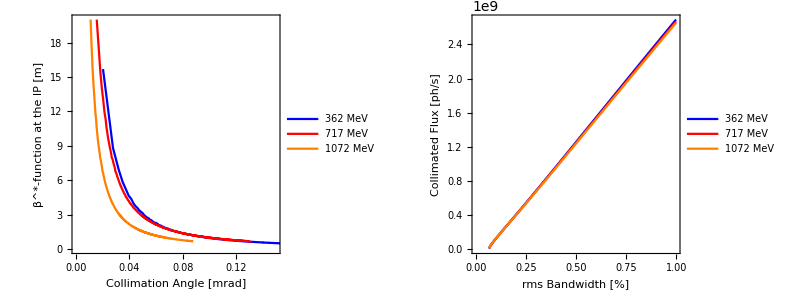

```mathematica
DIANARBplot=Grid[{{DIANARBβθ,DIANARBFBW}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAcomp"];
Export["DIANARBplot.png",DIANARBplot];
Export["DIANARBplot.pdf",DIANARBplot];
```

## DIANA 1072 Crab Crossing Comparison (Simplex NRB, GA NRB)

## Single rms Bandwidth

```mathematica
(*NRB SIMPLEX DATA*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA1072RMS05NRB=<<"RMSDIANA1072-0.5BW-Grid.txt";
DIANA1072RMS1NRB=<<"RMSDIANA1072-1BW-Grid.txt";

DIANA1072RMS05NRBCC=<<"RMSDIANA1072-CC-0.5BW-Grid.txt";
DIANA1072RMS1NRBCC=<<"RMSDIANA1072-CC-1BW-Grid.txt";
```

```mathematica
Grid[{{DIANA1072RMS05NRB,DIANA1072RMS05NRBCC},{DIANA1072RMS1NRB,DIANA1072RMS1NRBCC}}]
```

RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.500004 | %
Collimation Angle | θ_col | 0.0613261 | mrad
β_x-function at the IP | (β^*)_x | 3.8987 | m
β_y-function at the IP | (β^*)_y | 0.874234 | m
Collimated Flux | F_col | 1.28563×10^9 | ph/s
Simulation Time | t_sim | 98.7978 | s | RMS Optimisation (Crab Crossing) |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 0.5 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 0.500004 | %
Collimation Angle | θ_col | 0.0597531 | mrad
β_x-function at the IP | (β^*)_x | 0.917586 | m
β_y-function at the IP | (β^*)_y | 0.917587 | m
Collimated Flux | F_col | 1.11787×10^10 | ph/s
Simulation Time | t_sim | 95.3379 | s
RMS Optimisation |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.0882406 | mrad
β_x-function at the IP | (β^*)_x | 2.38678 | m
β_y-function at the IP | (β^*)_y | 0.51783 | m
Collimated Flux | F_col | 2.72978×10^9 | ph/s
Simulation Time | t_sim | 101.258 | s | RMS Optimisation (Crab Crossing) |  |  | 
Parameter | Symbol | Value | Unit
RMS Target Bandwidth | (ΔE_γ/E_γ)_RMS | 1 | %
RMS Achieved Bandwidth | (ΔE_γ/E_γ)_RMS | 1. | %
Collimation Angle | θ_col | 0.0866271 | mrad
β_x-function at the IP | (β^*)_x | 0.537591 | m
β_y-function at the IP | (β^*)_y | 0.53759 | m
Collimated Flux | F_col | 2.53765×10^10 | ph/s
Simulation Time | t_sim | 93.3845 | s

```mathematica
{DIANA1072RMS05NRBCC⟦1,8,3⟧/DIANA1072RMS05NRB⟦1,8,3⟧,DIANA1072RMS1NRBCC⟦1,8,3⟧/DIANA1072RMS1NRB⟦1,8,3⟧}
```

{8.69509,9.29616}

## Input Data

```mathematica
(*DATA ENTRY: SIMPLEX, RB, GA*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Simplex_TuningDat/DIANA"];
DIANA1072RMSCC=<<"DIANA1072simplexRMSCC.txt";
DIANA1072RMS=<<"DIANA1072simplexRMS.txt";

SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA1072BFRBCC=<<"DIANA1072optRMSCC.txt";
DIANA1072BFRB=<<"DIANA1072optRMS.txt";

DIANA1072CCGANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANA_CrabCavity/DIANA1072_CC_pareto.200.50","Table"];
DIANA1072GANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA1072_pareto.200","Table"];
```

## rms Tuning Curve Comparison (Crab vs None) (Simplex NRB)

```mathematica
βyrb[βxrb_]:=βxrb;
```

```mathematica
βxβyRB=Table[{βxrb,βyrb[βxrb]},{βxrb,0,20,0.01}];
```

```mathematica
BWach[BWlin_]:=BWlin;
BWlinear=Table[{BWlin,BWach[BWlin]},{BWlin,0,1,0.01}];
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
CCvsNRBFBWplot=ListPlot[{Partition[Riffle[DIANA1072RMSCC⟦2,All,3⟧,DIANA1072RMSCC⟦2,All,2,1⟧],2],Partition[Riffle[DIANA1072RMS⟦2,All,3⟧,DIANA1072RMS⟦2,All,2,1⟧],2]},PlotStyle->{{PointSize[0.015],Red},{PointSize[0.015],Blue}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (Sim NRB)","None (Sim NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],ImageSize->Medium,PlotRange->{{0,1},{0,2.7*10^10}}];
```

```mathematica
CCvsNRBBWachBWtarplot=ListPlot[{BWlinear,Partition[Riffle[DIANA1072RMSCC⟦2,All,1⟧,DIANA1072RMSCC⟦2,All,3⟧],2],Partition[Riffle[DIANA1072RMS⟦2,All,1⟧,DIANA1072RMS⟦2,All,3⟧],2]},Joined->{True,False,False},PlotStyle->{Black,{PointSize[0.015],Red},{PointSize[0.015],Blue}},Frame->True,FrameLabel->{"rms Target Bandwidth [%]","rms Achieved Bandwidth [%]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"BW_ach=BW_tar","Crab (Sim NRB)","None (Sim NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],ImageSize->Medium,PlotRange->{{0,1},{0,1}}];
```

```mathematica
CCvsNRBθcolβxplot=ListPlot[{Partition[Riffle[DIANA1072RMSCC⟦2,All,2,2,1,2⟧/mrad,DIANA1072RMSCC⟦2,All,2,2,2,2⟧],2],Partition[Riffle[DIANA1072RMS⟦2,All,2,2,1,2⟧/mrad,DIANA1072RMS⟦2,All,2,2,2,2⟧],2]},PlotStyle->{{PointSize[0.015],Red},{PointSize[0.015],Blue}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (Sim NRB)","None (Sim NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.8}],ImageSize->Medium,PlotRange->{{0,0.1},{0,20}}];
```

```mathematica
CCvsNRBθcolβyplot=ListPlot[{Partition[Riffle[DIANA1072RMSCC⟦2,All,2,2,1,2⟧/mrad,DIANA1072RMSCC⟦2,All,2,2,3,2⟧],2],Partition[Riffle[DIANA1072RMS⟦2,All,2,2,1,2⟧/mrad,DIANA1072RMS⟦2,All,2,2,3,2⟧],2]},PlotStyle->{{PointSize[0.015],Red},{PointSize[0.015],Blue}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (Sim NRB)","None (Sim NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.38,0.8}],ImageSize->Medium,PlotRange->{{0,0.1},{0,15}}];
```

```mathematica
CCvsNRBβxβyplot=ListPlot[{Partition[Riffle[DIANA1072RMSCC⟦2,All,2,2,2,2⟧,DIANA1072RMSCC⟦2,All,2,2,3,2⟧],2],Partition[Riffle[DIANA1072RMS⟦2,All,2,2,2,2⟧,DIANA1072RMS⟦2,All,2,2,3,2⟧],2],βxβyRB},Joined->{False,False,True},PlotStyle->{{PointSize[0.015],Red},{PointSize[0.015],Blue},Black},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (Sim NRB)","None (Sim NRB)","None (RB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

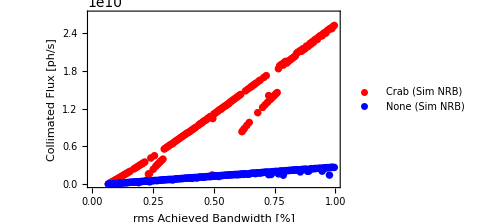
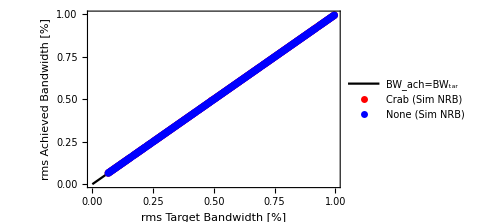
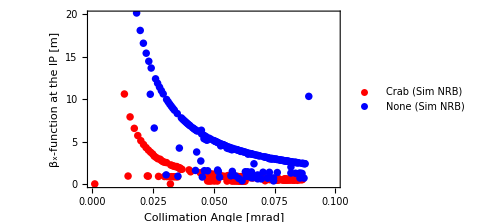
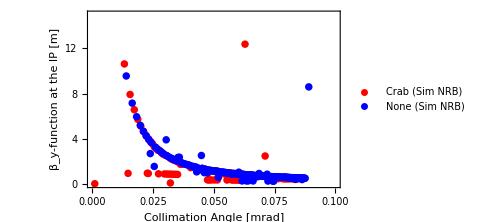
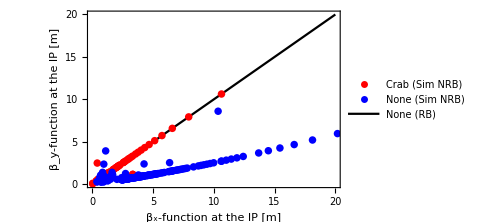
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{CCvsNRBFBWplot,CCvsNRBBWachBWtarplot},{CCvsNRBθcolβxplot,CCvsNRBθcolβyplot,CCvsNRBβxβyplot}}]
```

## rms Tuning Curve Comparison (Crab vs None) (GA NRB)

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
CCvsGANRBFBWplot=ListPlot[{Partition[Riffle[DIANA1072CCGANRB⟦All,2⟧,-DIANA1072CCGANRB⟦All,3⟧],2],Partition[Riffle[DIANA1072GANRB⟦All,2⟧,-DIANA1072GANRB⟦All,3⟧],2]},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (GA NRB)","None (GA NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,2.6*10^10}},ImageSize->Medium];
```

```mathematica
CCvsGANRBθcolβxplot=ListPlot[{Partition[Riffle[DIANA1072CCGANRB⟦All,4⟧,DIANA1072CCGANRB⟦All,5⟧],2],Partition[Riffle[DIANA1072GANRB⟦All,4⟧,DIANA1072GANRB⟦All,5⟧],2]},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (GA NRB)","None (GA NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
CCvsGANRBθcolβyplot=ListPlot[{Partition[Riffle[DIANA1072CCGANRB⟦All,4⟧,DIANA1072CCGANRB⟦All,6⟧],2],Partition[Riffle[DIANA1072GANRB⟦All,4⟧,DIANA1072GANRB⟦All,6⟧],2]},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (GA NRB)","None (GA NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
CCvsGANRBβxβyplot=ListPlot[{Partition[Riffle[DIANA1072CCGANRB⟦All,5⟧,DIANA1072CCGANRB⟦All,6⟧],2],βxβyRB,Partition[Riffle[DIANA1072GANRB⟦All,5⟧,DIANA1072GANRB⟦All,6⟧],2]},Joined->{False,True},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (GA NRB)","None (RB)","None (GA NRB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

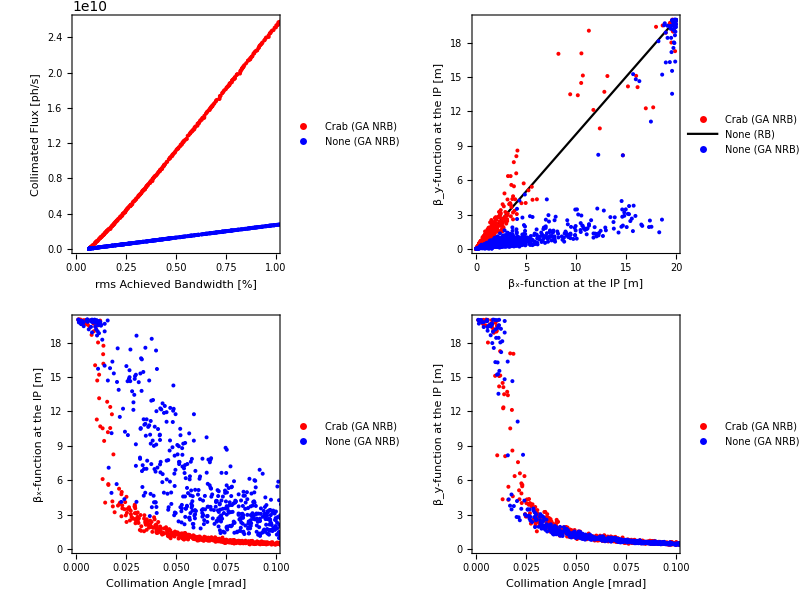

```mathematica
Grid[{{CCvsGANRBFBWplot,CCvsGANRBβxβyplot},{CCvsGANRBθcolβxplot,CCvsGANRBθcolβyplot}}]
```

## rms Tuning Curve Comparison (Crab vs None) (RB)

```mathematica
CCvsRBFBWplot=ListPlot[{Partition[Riffle[DIANA1072BFRBCC⟦All,1⟧,DIANA1072BFRBCC⟦All,4⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,1⟧,DIANA1072BFRB⟦All,4⟧],2]},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (RB)","None (RB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,2.6*10^10}},ImageSize->Medium];
```

```mathematica
CCvsRBθcolβplot=ListPlot[{Partition[Riffle[DIANA1072BFRBCC⟦All,2⟧,DIANA1072BFRBCC⟦All,3⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,2⟧,DIANA1072BFRB⟦All,3⟧],2]},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (RB)","None (RB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
CCvsRBβxβyplot=ListPlot[{Partition[Riffle[DIANA1072BFRBCC⟦All,3⟧,DIANA1072BFRBCC⟦All,3⟧],2],Partition[Riffle[DIANA1072BFRB⟦All,3⟧,DIANA1072BFRB⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Crab (RB)","None (RB)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

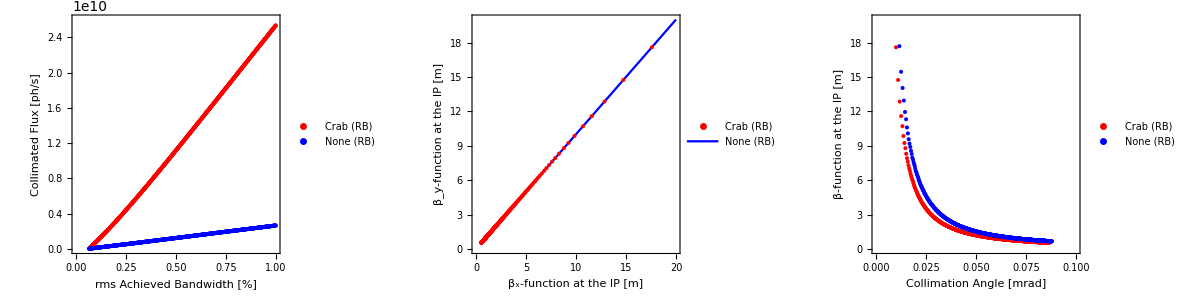

```mathematica
Grid[{{CCvsRBFBWplot,CCvsRBβxβyplot,CCvsRBθcolβplot}}]
```

## Thesis Case A

## Case Input

```mathematica
(*GA NRB*)
CaseAGANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/GA_NRB/Case_A_Pareto.200.50","Table"];
(*SIMPLEX NRB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/simplex_NRB"];
CaseASNRB=<<"CaseAsimplexRMS.txt";
(*BRUTE FORCE RB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/RB"];
CaseABFRB=<<"CaseAoptRMS.txt";
```

## Case A Comparison

```mathematica
CaseAFBWcomp=ListPlot[{Partition[Riffle[CaseAGANRB⟦All,2⟧,-CaseAGANRB⟦All,3⟧],2],Partition[Riffle[CaseABFRB⟦All,1⟧,CaseABFRB⟦All,4⟧],2],Partition[Riffle[CaseASNRB⟦2,All,3⟧,CaseASNRB⟦2,All,2,1⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,2*10^9}},ImageSize->Medium];
```

```mathematica
CaseAθcolβxcomp=ListPlot[{Partition[Riffle[CaseAGANRB⟦All,4⟧,CaseAGANRB⟦All,5⟧],2],Partition[Riffle[CaseABFRB⟦All,2⟧,CaseABFRB⟦All,3⟧],2],Partition[Riffle[CaseASNRB⟦2,All,2,2,1,2⟧/mrad,CaseASNRB⟦2,All,2,2,2,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
CaseAθcolβycomp=ListPlot[{Partition[Riffle[CaseAGANRB⟦All,4⟧,CaseAGANRB⟦All,6⟧],2],Partition[Riffle[CaseABFRB⟦All,2⟧,CaseABFRB⟦All,3⟧],2],Partition[Riffle[CaseASNRB⟦2,All,2,2,1,2⟧/mrad,CaseASNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.1},{0,20}},ImageSize->Medium];
```

```mathematica
CaseAβxβycomp=ListPlot[{Partition[Riffle[CaseAGANRB⟦All,5⟧,CaseAGANRB⟦All,6⟧],2],βxβyRB,Partition[Riffle[CaseASNRB⟦2,All,2,2,2,2⟧,CaseASNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,True,False},PlotStyle->{{Red,PointSize[0.008]},Black,{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

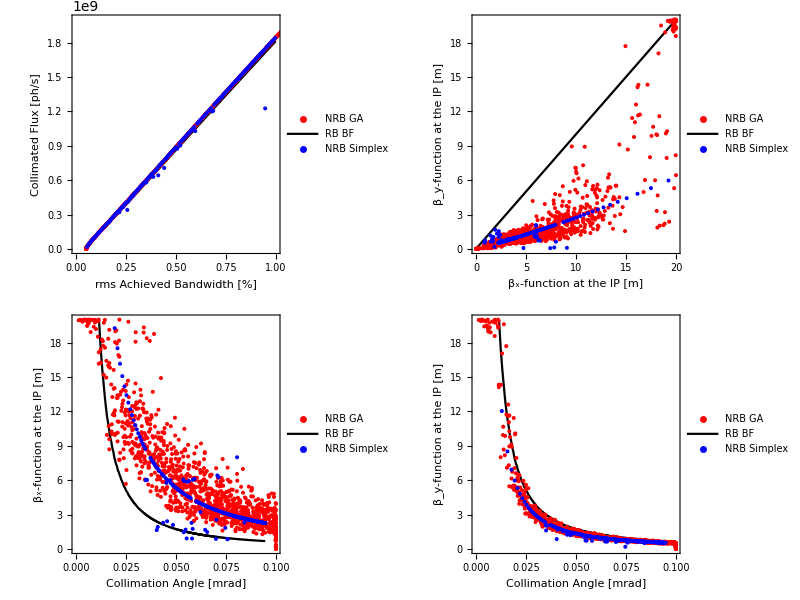

```mathematica
CaseAcomp=Grid[{{CaseAFBWcomp,CaseAβxβycomp},{CaseAθcolβxcomp,CaseAθcolβycomp}}]
```

## Plot Export

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/Thesis_Comparison_Plots"];
Export["CaseAcomp.png",CaseAcomp];
Export["CaseAcomp.pdf",CaseAcomp];
```

## Thesis Case B

## Case Input

```mathematica
(*GA NRB*)
CaseBGANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/GA_NRB/Case_B_Pareto.200.50","Table"];
(*SIMPLEX NRB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/simplex_NRB"];
CaseBSNRB=<<"CaseBsimplexRMS.txt";
(*BRUTE FORCE RB*)
(*SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/RB"];
CaseBBFRB=<<"CaseBoptRMS.txt";*)
```

## Case B Comparison

```mathematica
CaseBFBWcomp=ListPlot[{Partition[Riffle[CaseBGANRB⟦All,2⟧,-CaseBGANRB⟦All,3⟧],2],Partition[Riffle[CaseBSNRB⟦2,All,3⟧,CaseBSNRB⟦2,All,2,1⟧],2]},Joined->{False,False},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,2},{0,1.1*10^10}},ImageSize->Medium];
```

```mathematica
CaseBθcolβxcomp=ListPlot[{Partition[Riffle[CaseBGANRB⟦All,4⟧,CaseBGANRB⟦All,5⟧],2],Partition[Riffle[CaseBSNRB⟦2,All,2,2,1,2⟧/mrad,CaseBSNRB⟦2,All,2,2,2,2⟧],2]},Joined->{False,False},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.8}],PlotRange->{{0,0.25},{0,30}},ImageSize->Medium];
```

```mathematica
CaseBθcolβycomp=ListPlot[{Partition[Riffle[CaseBGANRB⟦All,4⟧,CaseBGANRB⟦All,6⟧],2],Partition[Riffle[CaseBSNRB⟦2,All,2,2,1,2⟧/mrad,CaseBSNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,False},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,0.25},{0,30}},ImageSize->Medium];
```

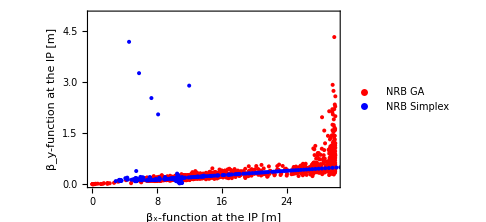

```mathematica
CaseBβxβycomp=ListPlot[{Partition[Riffle[CaseBGANRB⟦All,5⟧,CaseBGANRB⟦All,6⟧],2],Partition[Riffle[CaseBSNRB⟦2,All,2,2,2,2⟧,CaseBSNRB⟦2,All,2,2,3,2⟧],2]},Joined->{False,False},PlotStyle->{{Red,PointSize[0.008]},{Blue,PointSize[0.008]}},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","NRB Simplex"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.75}],PlotRange->{{0,30},{0,5}},ImageSize->Medium]
```

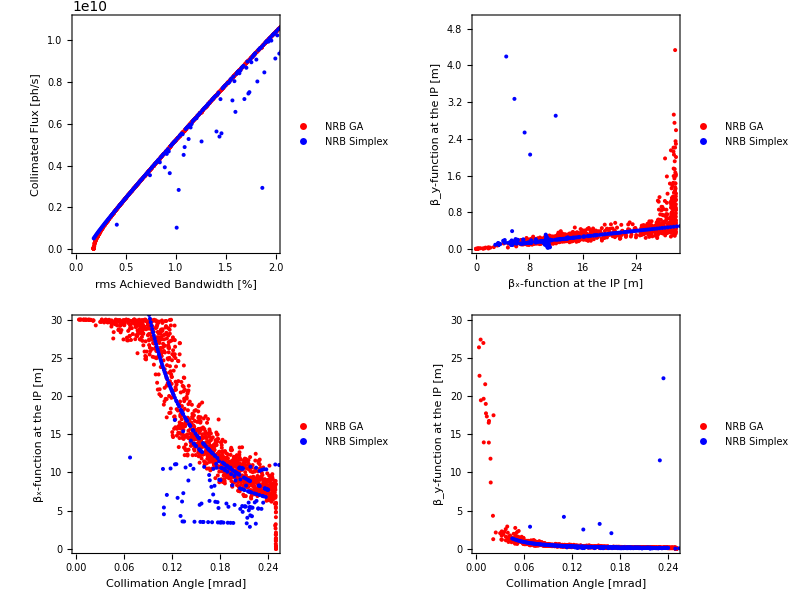

```mathematica
CaseBcomp=Grid[{{CaseBFBWcomp,CaseBβxβycomp},{CaseBθcolβxcomp,CaseBθcolβycomp}}]
```

## Plot Export

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/Thesis_Comparison_Plots"];
Export["CaseBcomp.png",CaseBcomp];
Export["CaseBcomp.pdf",CaseBcomp];
```

## Thesis Case C

## Case Input

```mathematica
(*GA NRB*)
CaseCGANRB=Import["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/GA_NRB/Case_C_Pareto.200.50","Table"];
(*SIMPLEX NRB*)
(*SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/simplex_NRB"];
CaseCSNRB=<<"CaseCsimplexRMS.txt";*)
(*BRUTE FORCE RB*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/RB"];
CaseCBFRB=<<"CaseCoptRMS.txt";
```

## Case A Comparison

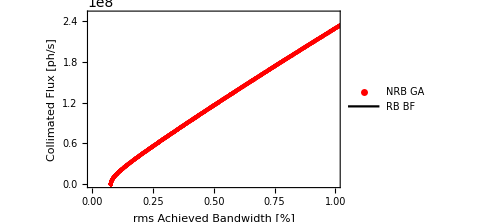

```mathematica
CaseCFBWcomp=ListPlot[{Partition[Riffle[CaseCGANRB⟦All,2⟧,-CaseCGANRB⟦All,3⟧],2],Partition[Riffle[CaseCBFRB⟦All,1⟧,CaseCBFRB⟦All,4⟧],2](*,Partition[Riffle[CaseCSNRB⟦2,All,3⟧,CaseCSNRB⟦2,All,2,1⟧],2]*)},Joined->{False,True(*,False*)},PlotStyle->{{Red,PointSize[0.008]},Black(*,{Blue,PointSize[0.008]}*)},Frame->True,FrameLabel->{"rms Achieved Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF"(*,"NRB Simplex"*)},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,1},{0,2.5*10^8}},ImageSize->Medium]
```

```mathematica
CaseCθcolβxcomp=ListPlot[{Partition[Riffle[CaseCGANRB⟦All,4⟧,CaseCGANRB⟦All,5⟧],2],Partition[Riffle[CaseCBFRB⟦All,2⟧,CaseCBFRB⟦All,3⟧],2](*,Partition[Riffle[CaseCSNRB⟦2,All,2,2,1,2⟧/mrad,CaseCSNRB⟦2,All,2,2,2,2⟧],2]*)},Joined->{False,True(*,False*)},PlotStyle->{{Red,PointSize[0.008]},Black(*,{Blue,PointSize[0.008]}*)},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF"(*,"NRB Simplex"*)},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,4},{0,20}},ImageSize->Medium];
```

```mathematica
CaseCθcolβycomp=ListPlot[{Partition[Riffle[CaseCGANRB⟦All,4⟧,CaseCGANRB⟦All,6⟧],2],Partition[Riffle[CaseCBFRB⟦All,2⟧,CaseCBFRB⟦All,3⟧],2](*,Partition[Riffle[CaseCSNRB⟦2,All,2,2,1,2⟧/mrad,CaseCSNRB⟦2,All,2,2,3,2⟧],2]*)},Joined->{False,True(*,False*)},PlotStyle->{{Red,PointSize[0.008]},Black(*,{Blue,PointSize[0.008]}*)},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF"(*,"NRB Simplex"*)},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.75,0.7}],PlotRange->{{0,4},{0,12}},ImageSize->Medium];
```

```mathematica
CaseCβxβycomp=ListPlot[{Partition[Riffle[CaseCGANRB⟦All,5⟧,CaseCGANRB⟦All,6⟧],2],βxβyRB(*,Partition[Riffle[CaseCSNRB⟦2,All,2,2,2,2⟧,CaseCSNRB⟦2,All,2,2,3,2⟧],2]*)},Joined->{False,True(*,False*)},PlotStyle->{{Red,PointSize[0.008]},Black(*,{Blue,PointSize[0.008]}*)},Frame->True,FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"NRB GA","RB BF"(*,"NRB Simplex"*)},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.25,0.75}],PlotRange->{{0,20},{0,20}},ImageSize->Medium];
```

```mathematica
CaseCcomp=Grid[{{CaseAFBWcomp,CaseAβxβycomp},{CaseAθcolβxcomp,CaseAθcolβycomp}}]
```

-Graphics-

## Plot Export

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Opt_Char_Data/Tuning_Curve/Thesis_Comparison_Plots"];
Export["CaseAcomp.png",CaseAcomp];
Export["CaseAcomp.pdf",CaseAcomp];
```